# Constante de Feigenbaum

## Nombre des lapins

On veut trouver quelle sera le nombre des lapins apres n annees.
				
				x_n = r * x_(n-1)                          -pas tres bonne


			x_n = r_(n-1) * x_(n-1)*(1-x_(n-1))
r_(n =)r_(n-1)+ E

r - coeff de multiplication de lapins
x_n-le nombre de lapins de l'annee n

```mathematica
mytable = {};
For[r=0,r<6,r+=0.01,
	x = {0.5};
	For[i=2, i≤80, i++,
		 If[x[[i-1]]>0.001, 
			AppendTo[x,r*x[[i-1]]*(1-x[[i-1]])],
			AppendTo[x,0]]
             ]
    AppendTo[mytable, x]
]
```

```mathematica
Manipulate[ListLinePlot[mytable⟦r⟧,AxesLabel->{"n","x_n"},PlotLabel->{{"Coeff de multiplication"},{ r/100}},LabelStyle->Directive[Bold, Black], PlotRange->{{0,80},{0,1}}],{r,1,600},AutoAction->False]
```

Part::partd: Part specification mytable⟦600.⟧ is longer than depth of object.

ListLinePlot::lpn: mytable⟦600.⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mytable⟦197.⟧ is longer than depth of object.

ListLinePlot::lpn: mytable⟦197.⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification mytable⟦397.⟧ is longer than depth of object.

ListLinePlot::lpn: mytable⟦397.⟧ is not a list of numbers or pairs of numbers.

```mathematica
mylist={};
For[r=1,r<600,r+=1,
AppendTo[mylist,mytable[[r]][[80]] ]
]
mylist2={};
For[r=1,r<600,r+=1,
AppendTo[mylist2,mytable[[r]][[79]] ]
]
mylist3={};
For[r=1,r<600,r+=1,
AppendTo[mylist3,mytable[[r]][[78]] ]
]
mylist4={};
For[r=1,r<600,r+=1,
AppendTo[mylist4,mytable[[r]][[77]] ]
]
mylist5={};
For[r=1,r<600,r+=1,
AppendTo[mylist5,mytable[[r]][[76]] ]
]
mylist6={};
For[r=1,r<600,r+=1,
AppendTo[mylist6,mytable[[r]][[75]] ]
]
mylist7={};
For[r=1,r<600,r+=1,
AppendTo[mylist7,mytable[[r]][[74]] ]
]
mylist8={};
For[r=1,r<600,r+=1,
AppendTo[mylist8,mytable[[r]][[73]] ]
]
```

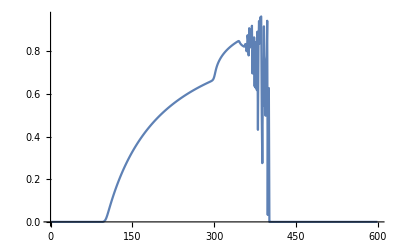

```mathematica
ListLinePlot[mylist]
```

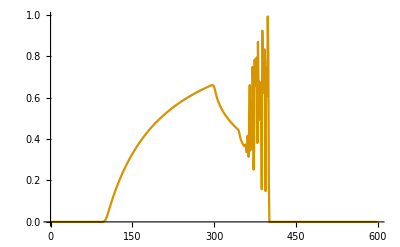

```mathematica
ListLinePlot[mylist2,PlotStyle->RGBColor[0.84,0.58,0.]]
```

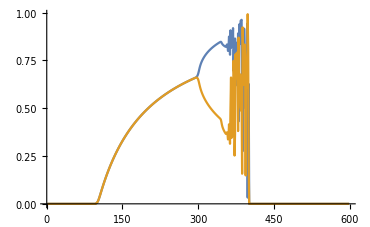

```mathematica
ListLinePlot[{mylist,mylist2}]
```

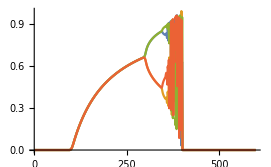

```mathematica
ListLinePlot[{mylist,mylist2,mylist3,mylist4}]
```

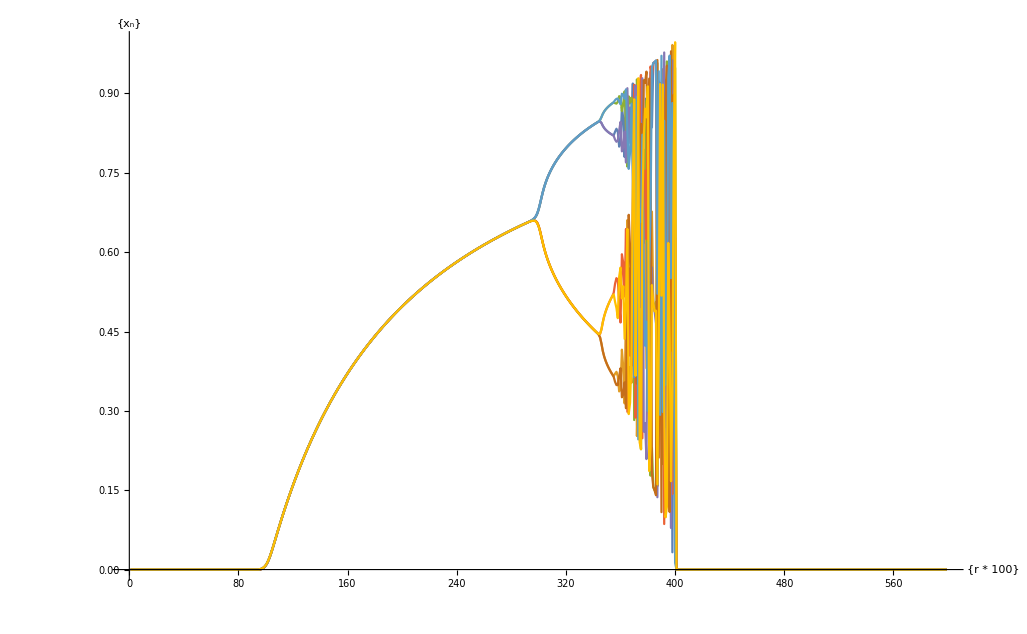

```mathematica
ListLinePlot[{mylist,mylist2,mylist3,mylist4,mylist5,mylist6,mylist7,mylist8}, AxesLabel->{{"r * 100"},{"x_n"}}]
```

```mathematica
break = {295.2,344.4,355,357.3};
break1 = Line[{{break[[1]],0},{break[[1]],1}}];
break2 = Line[{{break[[2]],0},{break[[2]],1}}];
break3 = Line[{{break[[3]],0},{break[[3]],1}}];
break4 = Line[{{break[[4]],0},{break[[4]],1}}];
ListLinePlot[{mylist,mylist2,mylist3,mylist4,mylist5,mylist6,mylist7,mylist8}, AxesLabel->{{"r * 100"},{"x_n"}}, Epilog->{break1,break2,break3,break4}]
```

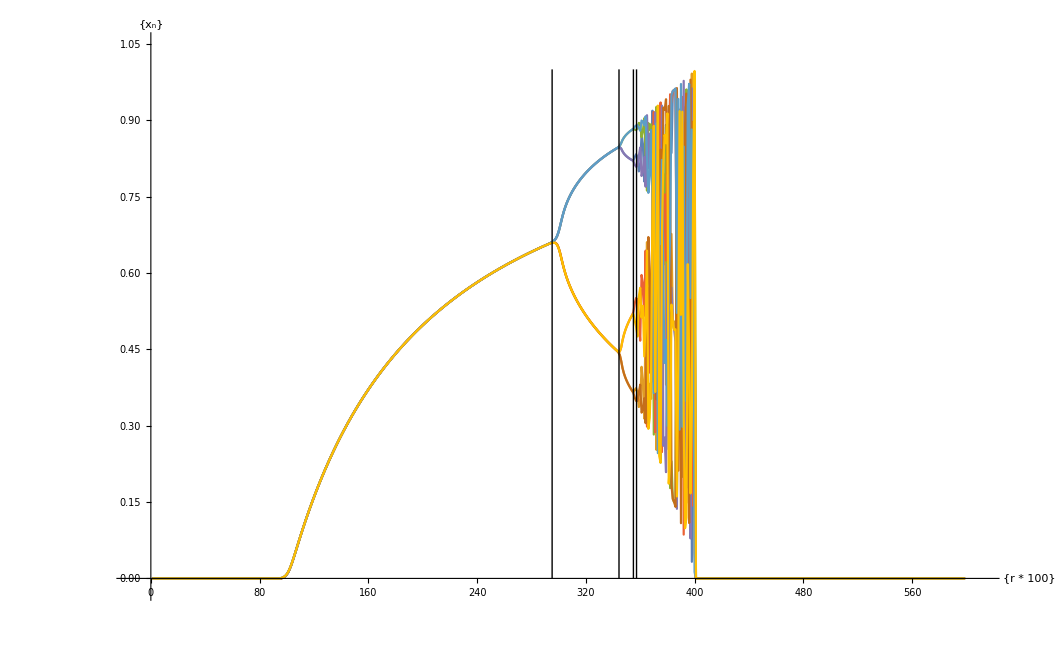

```mathematica
(break[[2]]-break[[1]])/(break[[3]]-break[[2]])//N

(break[[3]]-break[[2]])/(break[[4]]-break[[3]])//N
```

```mathematica
4.6415
```

4.6087

RecurrenceTable::dsfun: 0.5 cannot be used as a function.

General::stop: Further output of RecurrenceTable::dsfun will be suppressed during this calculation.

-Graphics-